# Discrete Power-law fitter

```mathematica
Needs["ProgressMapping`",FileNameJoin[{NotebookDirectory[],"ProgressMapping.wl"}]]
```

```mathematica
DiscretePowerLawDistributionPDF[α_,xMin_,x_]:=x^-α/HurwitzZeta[α,xMin];
DiscretePowerLawDistributionCDF[α_,xMin_,x_]:=HurwitzZeta[α,x]/HurwitzZeta[α,xMin];
EmpiricalCDF[data_,x_]:= N[1-CDF[EmpiricalDistribution[data],x]];
GeneratePowerlawSampleData[α_,xMin_,xMax_,sampleSize_ :1000]:=Block[{dist},
dist = ProbabilityDistribution[DiscretePowerLawDistributionPDF[α,xMin,x],{x,xMin,xMax,1}];

RandomVariate[dist,sampleSize]

];
```

```mathematica
SelectTail[data_,xMin_]:=Select[data,#>=xMin&];
SelectBulk[data_,xMin_]:=Select[data,#<xMin&];
Estimateα[data_,xMin_]:=Block[{n,tail},
tail = SelectTail[data,xMin];
n = Length[tail];
N[1 + n (∑_(i=1)^n Log[tail[[i]]/(xMin-1/2)])^-1]
];
```

```mathematica
KSStatistic[data_,xMin_Integer]:=Block[{xMax,tail,αEstimator,diff},
tail = SelectTail[data,xMin];
αEstimator = Estimateα[data,xMin];
xMax = Max[data];
diff = Table[Abs[EmpiricalCDF[tail,x]-DiscretePowerLawDistributionCDF[αEstimator,xMin,x]],{x,xMin,xMax}];
Max[diff]
];
KSStatistic[data_,model_Association]:=Block[{xMax,tail,αEstimator,diff},
tail = SelectTail[data,model["xMin"]];
αEstimator = model["Alpha"];
xMax = Max[data];
diff = Table[Abs[EmpiricalCDF[tail,x]-DiscretePowerLawDistributionCDF[αEstimator,model["xMin"],x]],{x,model["xMin"],xMax}];
Max[diff]
];
KSStatistic[data_]:=KSStatistic[data,EstimateαAndXMin[data]];
EstimateαAndXMin[data_]:=Block[{minElement,maxElement,xMin,α},
{minElement,maxElement} = MinMax[data];
xMin = MinimalBy[Table[{x,KSStatistic[data,x]},{x,minElement,maxElement}],Last][[1,1]];
α = Estimateα[data,xMin];
<|"Alpha"->α, "xMin"->xMin|>
];
GenerateBootstrapReplica[data_,model_]:=Block[{n,bulk, tail,tailProbability,tailReplica,bulkReplica},
n = Length[data];
bulk = SelectBulk[data,model["xMin"]];
tail = SelectTail[data,model["xMin"]];
tailProbability = 1.0 - Length[bulk]/n;
tailReplica = GeneratePowerlawSampleData[model["Alpha"],model["xMin"],Max[data],Floor[n*tailProbability]];
bulkReplica = RandomSample[bulk,n-Floor[n*tailProbability]];
RandomSample[Join[tailReplica, bulkReplica]]
];
CalculateGOF[data_,replicas_:2000]:=Block[{model,ksOfData,syntheticKsValues,pValue},
model = EstimateαAndXMin[data];
ksOfData = KSStatistic[data,model];
syntheticKsValues = ProgressTable[KSStatistic[GenerateBootstrapReplica[data,model]],replicas];
pValue = N[Count[syntheticKsValues,x_ /; x>ksOfData]/Length[syntheticKsValues]];
<|"Alpha"->model["Alpha"],"xMin"->model["xMin"],"p-value"->pValue|>
];
```

```mathematica
sample = GeneratePowerlawSampleData[2.5,1,100,200]
```

{1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,1,1,3,1,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,1,3,1,1,1,1,1,1,3,1,5,1,2,1,2,1,1,2,3,1,1,1,1,1,1,7,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,3,2,1,1,2,1,1,18,1,9,1,1,2,1,1,9,21,1,1,1,1,1,1,5,2,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,1,4,1,9,1,1,1,1,2,1,2,1,2,2,2,2,1,1,2,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,15,1,1,2,1,1,2,1,1,1,1,1,1,1,1,1,3}

```mathematica
Estimateα[sample,6]
```

2.33402

```mathematica
KSStatistic[sample,6]
```

0.19469

```mathematica
model = EstimateαAndXMin[sample]
```

<|Alpha→2.08014,xMin→4|>

```mathematica
ksOfSample = KSStatistic[sample,model]
```

0.158429

```mathematica
ksValues = ProgressTable[KSStatistic[GenerateBootstrapReplica[sample,model]],2000];
```

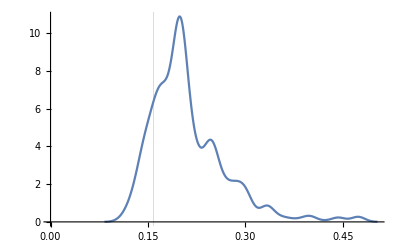

```mathematica
SmoothHistogram[ksValues,GridLines->{{ksOfSample},{}}]
```

```mathematica
N[Count[ksValues,x_ /; x>ksOfSample]/Length[ksValues]]
```

0.853

```mathematica
CalculateGOF[sample]
```

<|Alpha→2.08014,xMin→4,p-value→0.8395|>